### Steck 6.1: Gaussian 90-10 rule for getting w(z)

Find total power (confirm that it’s P)

```mathematica
Integrate[(2P)/(π w^2)Exp[-(2 r^2)/w^2]/.{r^2->x^2+y^2},{x,-∞,∞},{y,-∞,∞},Assumptions->{w>0}]
```

P

Integrate x only up to some special point x0

```mathematica
Px0=Integrate[(2P)/(π w^2)Exp[-(2 r^2)/w^2]/.{r^2->x^2+y^2},{x,-∞,x0},{y,-∞,∞},Assumptions->{w>0}]
```

1/2 P (1+Erf[(√2 x0)/w])

The picture actually shows the opposite, which is to integrate from a special point x0 to ∞.

```mathematica
Px0=Integrate[(2P)/(π w^2)Exp[-(2 r^2)/w^2]/.{r^2->x^2+y^2},{x,x0,∞},{y,-∞,∞},Assumptions->{w>0}]
```

1/2 P Erfc[(√2 x0)/w]

Plot that

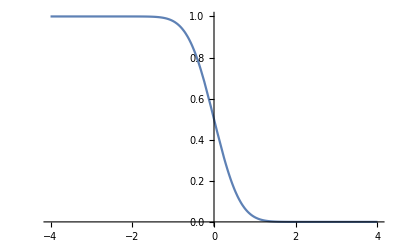

```mathematica
Plot[Px0/.{P->1,w->1},{x0,-4,4}]
```

Plot the error function itself

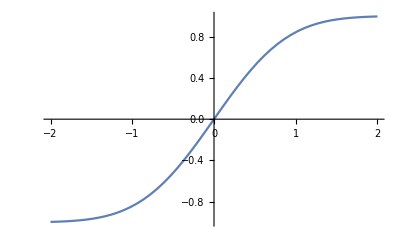

```mathematica
Plot[Erf[x],{x,-2,2}]
```

This is basically what you need to fit for in the lab, including an xoffset

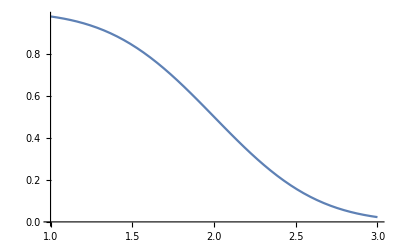

```mathematica
Plot[1/2 P (1-Erf[(√2 (x0-xcenter))/w])/.{P->1,w->1,xcenter->2},{x0,1,3}] (* for lab fit *)
```

Ok, no do the problem asked for, which is to solve for w when you know the 10% and 90% power positions.

```mathematica
x0sub=Solve[Px0==f P,x0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x0→(w InverseErfc[2 f])/(√2)}}

```mathematica
x10=(x0/.x0sub⟦1⟧/.f->1/10)
```

(w InverseErfc[1/5])/(√2)

```mathematica
x10//N
```

0.640776 w

```mathematica
InverseErfc[2 9/10]
```

-InverseErfc[1/5]

```mathematica
x90=(x0/.x0sub⟦1⟧/.f->9/10)
```

-(w InverseErfc[1/5])/(√2)

```mathematica
x9010=(x0/.x0sub⟦1⟧/.f->9/10)-(x0/.x0sub⟦1⟧/.f->1/10)
```

-√2 w InverseErfc[1/5]

```mathematica
√2 InverseErf[4/5]//N
```

1.28155

```mathematica
x9010//N
```

-1.28155 w

```mathematica
αsub=α->√2 InverseErf[4/5]//N
```

α→1.28155

Calculate w for the beam in the lab

```mathematica
(13.820-13.285)*α/.αsub
```

0.68563

Calculate a guess for xoffset for the lab

```mathematica
(13.820+13.285)/2
```

13.5525

### Steck 6.7: complex beam parameter

```mathematica
qsub=q->z-I z0
```

q→z-ⅈ z0

```mathematica
qsubcc=qcc->z+I z0
```

qcc→z+ⅈ z0

First look inside of exp() at

```mathematica
1/q/.qsub
```

1/(z-ⅈ z0)

Multiply top and bottom by qcc

```mathematica
num=qcc/.qsubcc//Expand
```

z+ⅈ z0

```mathematica
denom=q qcc/.qsub/.qsubcc//Expand
```

z^2+z0^2

```mathematica
realTerm=z/(z^2+z0^2)
```

z/(z^2+z0^2)

```mathematica
imagTerm=z0/(z^2+z0^2)
```

z0/(z^2+z0^2)

```mathematica
1/q==realTerm+I imagTerm/.qsub/.q0sub//Simplify
```

True

```mathematica
R[z_]:=z(1+(z0/z)^2)
```

```mathematica
realTerm==1/R[z]//Simplify
```

True

```mathematica
w[z_]:=w0 √(1+(z/z0)^2)
```

```mathematica
w0sub=w0->√((λ z0)/π)
```

w0→(√(z0 λ))/(√π)

```mathematica
ksub=k->(2π)/λ
```

k→(2 π)/λ

```mathematica
(I k r^2)/2(I imagTerm)==-r^2/w[z]^2/.w0sub/.ksub//Simplify
```

True

or a different way

```mathematica
λ/(π w[z]^2)
```

λ/(π w0^2 (1+z^2/z0^2))

```mathematica
imagTerm==λ/(π w[z]^2)/.w0sub//Simplify
```

True

Then look at outside term

```mathematica
q0sub=q0->0-I z0
```

q0→-ⅈ z0

```mathematica
q0/q/.qsub/.q0sub
```

-(ⅈ z0)/(z-ⅈ z0)

```mathematica
num=q0 qcc/.qsubcc/.q0sub//Expand
```

-ⅈ z z0+z0^2

```mathematica
denom=q qcc/.qsub/.qsubcc//Expand
```

z^2+z0^2

```mathematica
realTerm=z0^2/(z^2+z0^2)
```

z0^2/(z^2+z0^2)

```mathematica
imagTerm=(- z z0)/(z^2+z0^2)
```

-(z z0)/(z^2+z0^2)

```mathematica
q0/q==realTerm+I imagTerm/.qsub/.q0sub//Simplify
```

True

```mathematica
q0=q/.qsub/.z->0
```

-ⅈ z0

```mathematica
q0/(q/.qsub)
```

-(ⅈ z0)/(z-ⅈ z0)

```mathematica
q0overqMagnitudeSquared=(ⅈ z0)/(z-ⅈ z0)(-ⅈ z0)/(z+ⅈ z0)//FullSimplify
```

z0^2/(z^2+z0^2)

```mathematica
w0/w[z]
```

1/(√(1+z^2/z0^2))

```mathematica
w0overwSquared=(w0/w[z])^2//FullSimplify
```

1/(1+z^2/z0^2)

```mathematica
q0overqMagnitudeSquared==w0overwSquared//Simplify
```

True

```mathematica
q0overq=-(ⅈ z0(z+ⅈ z0))/((z-ⅈ z0)(z+ⅈ z0)//Expand)//Expand
```

-(ⅈ z z0)/(z^2+z0^2)+z0^2/(z^2+z0^2)

```mathematica
ArcTan[-z/z0]
```

1/R in terms of 1/q Steck eqn (6.40)

```mathematica
qsub=q->z-I z0
```

q→z-ⅈ z0

```mathematica
R[z_]:=z(1+(z0/z)^2)
```

```mathematica
w[z_]:=w0 √(1+(z/z0)^2)
```

```mathematica
w0sub=w0->√((λ z0)/π)
```

w0→(√(z0 λ))/(√π)

```mathematica
1/q-(1/R[z]+(ⅈ λ)/(π w[z]^2))/.qsub/.w0sub//FullSimplify
```

0